## Some setting

Data and plots

#### We have 10 data points

```mathematica
n=10;
```

#### Give the data

```mathematica
x=Table[i+RandomReal[], {i,0,10}]
```

{0.301554,1.51353,2.82512,3.8655,4.46734,5.26735,6.80425,7.35982,8.69651,9.10802,10.2167}

```mathematica
Mean[x]
```

5.49324

```mathematica
t=Table[ (x[[i]]*3+2)+RandomReal[{-2,2}],{i,1,10}]
```

{1.25094,6.05802,10.954,13.8093,15.242,18.6502,21.3727,23.5615,28.9253,29.8955}

```mathematica
l=Table[{x[[i]],t[[i]]},{i,1,10}]
```

{{0.301554,1.25094},{1.51353,6.05802},{2.82512,10.954},{3.8655,13.8093},{4.46734,15.242},{5.26735,18.6502},{6.80425,21.3727},{7.35982,23.5615},{8.69651,28.9253},{9.10802,29.8955}}

#### Plot of the data

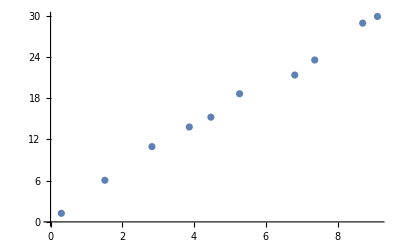

```mathematica
ListPlot[l]
```

#### Variance

```mathematica
σ=√Variance[t]
```

9.3748

#### The coefficient 3 is chosen by assumption in the next equation. It gives Log P(ω_i | t, x, σ)

```mathematica
term=1/(2 σ^2)(Sum[(t[[i]]-w0-w1 x[[i]])^2,{i,1,10}]+3(w0^2+w1^2))
```

0.00568913 ((29.8955-w0-9.10802 w1)^2+(28.9253-w0-8.69651 w1)^2+(23.5615-w0-7.35982 w1)^2+(21.3727-w0-6.80425 w1)^2+(18.6502-w0-5.26735 w1)^2+(15.242-w0-4.46734 w1)^2+(13.8093-w0-3.8655 w1)^2+(10.954-w0-2.82512 w1)^2+(6.05802-w0-1.51353 w1)^2+(1.25094-w0-0.301554 w1)^2+3 (w0^2+w1^2))

Posterior

#### Contour plot of P(ω_i | t, x, σ) , posterior

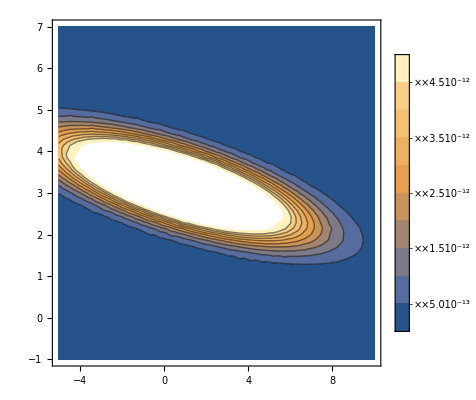

```mathematica
ContourPlot[(1/(2π σ))^(n/2+1)Exp[-term],{w0,-5,10},{w1,-1,7},PlotLegends->Automatic]
```

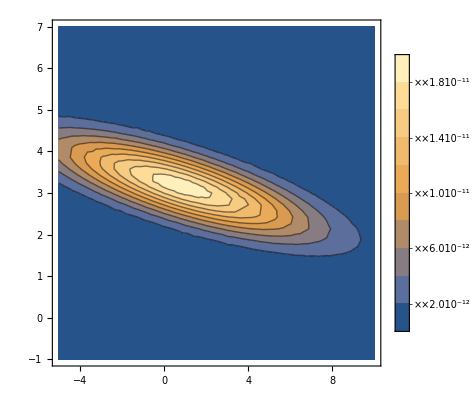

```mathematica
ContourPlot[(1/(2π σ))^(n/2+1)Exp[-term],{w0,-5,10},{w1,-1,7},PlotLegends->Automatic,PlotRange->{2*10^-11,0}]
```

#### Has a maximum at

```mathematica
Solve[{D[term,w0]==0,D[term,w1]==0},{w0,w1}]
```

{{w0→0.812961,w1→3.16977}}

#### Review for likelihood, Log P(t |ω,..)

```mathematica
original = 1/(2 σ^2)(Sum[(t[[i]]-w0-w1 x[[i]])^2,{i,1,10}])
```

0.00568913 ((29.8955-w0-9.10802 w1)^2+(28.9253-w0-8.69651 w1)^2+(23.5615-w0-7.35982 w1)^2+(21.3727-w0-6.80425 w1)^2+(18.6502-w0-5.26735 w1)^2+(15.242-w0-4.46734 w1)^2+(13.8093-w0-3.8655 w1)^2+(10.954-w0-2.82512 w1)^2+(6.05802-w0-1.51353 w1)^2+(1.25094-w0-0.301554 w1)^2)

```mathematica
Solve[{D[original,w0]==0,D[term,w1]==0},{w0,w1}]
```

{{w0→1.79794,w1→3.02217}}

#### Contour plot of P(t |ω,..), likelihood

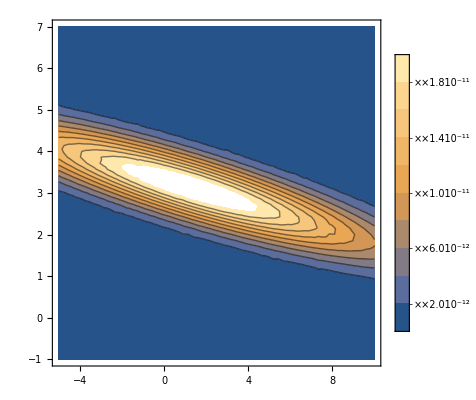

```mathematica
ContourPlot[(1/(2π σ))^(n/2+1)Exp[-original],{w0,-5,10},{w1,-1,7},PlotLegends->Automatic,PlotRange->{2*10^-11,0}]
```

Laplace approximation of posterior

#### Laplace approximation the constant factor.

```mathematica
G0=(1/(2π σ))^(n/2+1)Exp[-term]/.{w0->0.8129608926369966,w1->3.16977096459527}
```

1.93281×10^-11

```mathematica
P=(1/(2π σ))^(n/2+1)Exp[-term]
```

3.75562×10^-11 ⅇ^(-0.00661034 ((31.1715-w0-9.56193 w1)^2+(27.8925-w0-8.40024 w1)^2+(24.7902-w0-7.1589 w1)^2+(21.1721-w0-6.37539 w1)^2+(19.7597-w0-5.63943 w1)^2+(15.8388-w0-4.67881 w1)^2+(13.7288-w0-3.80613 w1)^2+(11.9761-w0-2.82883 w1)^2+(6.07394-w0-1.03325 w1)^2+(5.79229-w0-0.9665 w1)^2+(w0^2+w1^2)/(√3)))

#### Exponential part

```mathematica
D[D[-term,w0],w0]
```

-0.147917

```mathematica
D[D[-term,w0],w1]
```

-0.571291

```mathematica
D[D[-term,w1],w0]
```

-0.571291

```mathematica
D[D[-term,w1],w1]
```

-3.81237

```mathematica
A=({{D[D[-term,w0],w0], D[D[-term,w0],w1]}, {D[D[-term,w1],w0], D[D[-term,w1],w1]}})
```

{{-0.147917,-0.571291},{-0.571291,-3.81237}}

```mathematica
{{w0->0.8129608926369966,w1->3.16977096459527}}
```

```mathematica
({{w0-0.8129608926369966, w1-3.16977096459527}}).A.({{w0-0.8129608926369966}, {w1-3.16977096459527}})
```

{{(-0.812961+w0) (-0.147917 (-0.812961+w0)-0.571291 (-3.16977+w1))+(-0.571291 (-0.812961+w0)-3.81237 (-3.16977+w1)) (-3.16977+w1)}}

#### Full approximation

```mathematica
G=G0 Exp[(-0.8129608926369966+w0) (-0.1479173249248259 (-0.8129608926369966+w0)-0.5712906972305959 (-3.16977096459527+w1))+(-0.5712906972305959 (-0.8129608926369966+w0)-3.812366606111279 (-3.16977096459527+w1)) (-3.16977096459527+w1)]
```

1.93281×10^-11 ⅇ^((-0.812961+w0) (-0.147917 (-0.812961+w0)-0.571291 (-3.16977+w1))+(-0.571291 (-0.812961+w0)-3.81237 (-3.16977+w1)) (-3.16977+w1))

#### Contour plot of the Laplace approximation

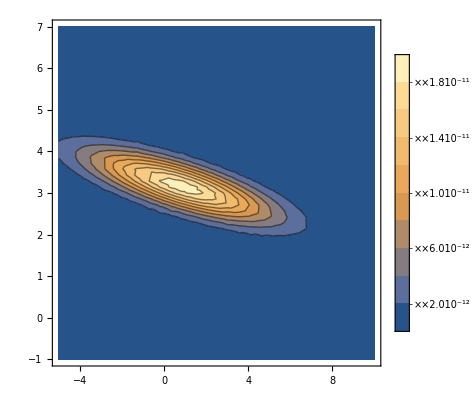

```mathematica
ContourPlot[G,{w0,-5,10},{w1,-1,7},PlotLegends->Automatic,PlotRange->{2*10^-11,0}]
```